```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={10119,10281,10497}];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
icycle=25;ChNum=4;binw=10;binw2=1;
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10119,10281,10497}

Size of event list in Cycle: 302005

Size of event list in Cycle: 602995

Size of event list in Cycle: 684002

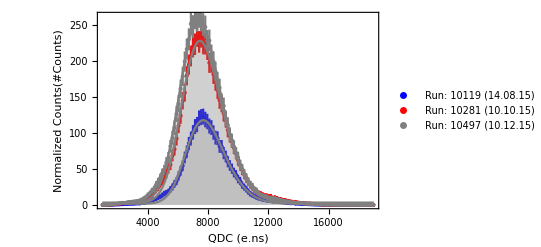

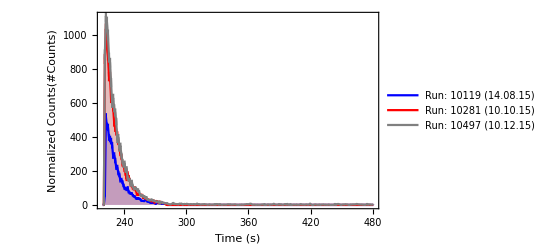

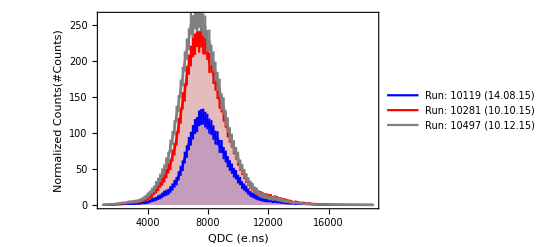

```mathematica
(*ucnw2={370059,884086,1224086};*)
ucnw2={1000000,1000000,1000000};
histbeg=70;histlast=1400;histbeg2=219;histlast2=481;
ptdat=Table[Table[{0,{0,0}},{k,1,Round[(histlast-histbeg)/binw]}],{l,1,Dimensions[runNum][[1]]}];
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,Dimensions[runNum][[1]]}];
fitparam=Table[{0,0,0,0,0},{k,1,Dimensions[runNum][[1]]}];
fiterror=Table[{0,0,0,0,0},{k,1,Dimensions[runNum][[1]]}];
For[runi=1,runi≤Dimensions[runNum][[1]],runi++,
Clear[data,histdata,nlm];data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
(*histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{100,3000,binw}];*)
histdata=HistogramList[data[[Round[1(*dimdata/1.022318*)];;dimdata,6]],{histbeg,histlast,binw}];
histdata2=HistogramList[data[[Round[dimdata/1.022318];;dimdata,4]]/1000000000,{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[runi]][[i]][[1]]=13.6*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[runi]][[i]][[2]][[1]]=10000*histdata[[2]][[i]]/ucnw2[[runi]];
ptdat[[runi]][[i]][[2]][[2]]=Sqrt[ptdat[[runi]][[i]][[2]][[1]]](*Sqrt[1/(100(1+histdata[[2]][[i]])/ucnw2[[runi]])]*);
];
(*Plot2-T*)
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[runi]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[runi]][[i]][[2]][[1]]=1000000*histdata2[[2]][[i]]/ucnw2[[runi]];
ptdat2[[runi]][[i]][[2]][[2]]=Sqrt[ptdat2[[runi]][[i]][[2]][[1]]];
];
(**)
nlm=NonlinearModelFit[Transpose[{ptdat[[runi,;;,1]],ptdat[[runi,;;,2,1]]}],(a+b PDF[SkewNormalDistribution[c,d,e],xx]),{{a,0},{e,2},{d,1000.},{c,7000},{b,10^5}},xx];
fitparam[[runi]]={a/.nlm[[1]][[2]],b/.nlm[[1]][[2]],c/.nlm[[1]][[2]],d/.nlm[[1]][[2]],e/.nlm[[1]][[2]]};
fiterror[[runi]]=nlm["ParameterErrors"];
];
Show[EDAListPlot[ptdat[[1]],ptdat[[2]],ptdat[[3]],PlotStyle->{Blue,Red,Gray},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 10119 (14.08.15)","Run: 10281 (10.10.15)","Run: 10497 (10.12.15)"},ImageSize->{1000}],Plot[Table[fitparam[[k]][[1]]+fitparam[[k]][[2]]PDF[SkewNormalDistribution[fitparam[[k]][[3]],fitparam[[k]][[4]],fitparam[[k]][[5]]],xx],{k,1,Dimensions[runNum][[1]]}],{xx,1000,19000},PlotStyle->{Blue,Red,Gray},Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]]
EDAListPlot[ptdat2[[1]],ptdat2[[2]],ptdat2[[3]],PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 10119 (14.08.15)","Run: 10281 (10.10.15)","Run: 10497 (10.12.15)"},ImageSize->{1000}]
EDAListPlot[ptdat[[1]],ptdat[[2]],ptdat[[3]],PlotStyle->{Blue,Red,Gray},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 10119 (14.08.15)","Run: 10281 (10.10.15)","Run: 10497 (10.12.15)"},ImageSize->{1000},Filling->Axis,Joined->True]
```

```mathematica
histdata2=HistogramList[data[[Round[dimdata/1.022318];;dimdata,4]]/1000000000,{219,481,1}];
ptdat2=Table[{0,{0,0}},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[i]][[2]]=2*histdata2[[2]][[i]];
];
ListLinePlot[{ptdat4,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 010119","Run: 010497"},Filling->Axis,ImageSize->{1000}]
Total[histdata2[[2]]]
```

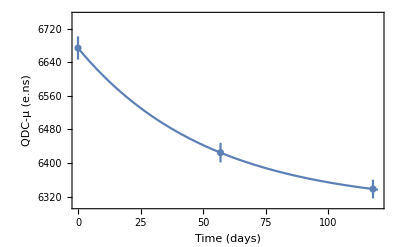

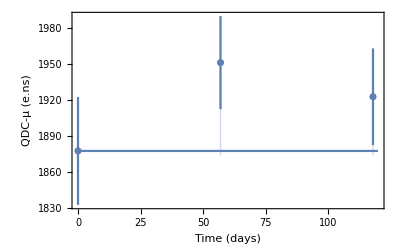

```mathematica
Show[{Plot[6298.846025973117+(fitparam[[;;,3]][[1]]-6298.846025973117)Exp[-0.01917354386801779t],{t,0,120},Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotRange->{{0,120},{6300,6750}}],EDAListPlot[Table[{{0,57,57+61}[[k]],Transpose[{fitparam[[;;,3]],fiterror[[;;,3]]}][[k]]},{k,1,3}],Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]},PlotRange->{{0,120},{6300,6750}}]
Show[{Plot[1877.4469822982524+(fitparam[[;;,4]][[1]]-1877.4469822982524)Exp[0.9978126153085122t],{t,0,120},Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotRange->{{0,120},{6300,6750}}],EDAListPlot[Table[{{0,57,57+61}[[k]],Transpose[{fitparam[[;;,4]],2fiterror[[;;,4]]}][[k]]},{k,1,3}],Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},Filling->Axis,ImageSize->{1000},PlotRange->{{0,120},{6300,6750}}]}]
```

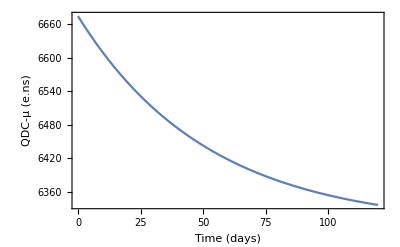

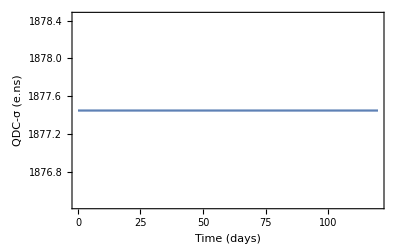

```mathematica
Plot[6298.846025973117+(fitparam[[;;,3]][[1]]-6298.846025973117)Exp[-0.01917354386801779t],{t,0,120},Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotRange->{{0,120},{6300,6750}}]
Plot[1877.4469822982524+(fitparam[[;;,4]][[1]]-1877.4469822982524)Exp[0.9978126153085122t],{t,0,120},Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-σ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotRange->{{0,120},{1500,3000}}]
```

```mathematica
Transpose[{fitparam[[;;,3]],fiterror[[;;,3]]}]
```

{{6674.11,28.2068},{6417.37,24.5527},{6317.42,22.0613}}

```mathematica
aa=Datum[{q,sq}]
bb=Datum[{w,sw}]
aa/bb
```

q±sq

w±sw

Datum[AdjustSignificantFigures[{1/w,Abs[sw/w^2]}]] (q±sq)

```mathematica
fitparam
```

{{1.75672,378931.,6674.11,1880.57,1.81282},{3.06819,764512.,6417.37,1956.88,1.81201},{2.90316,877666.,6317.42,1940.67,1.67237}}

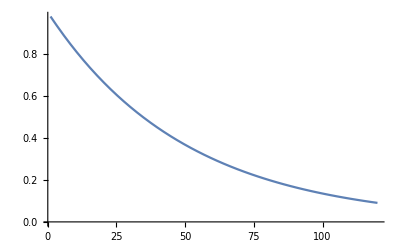

```mathematica
Plot[N[(-6000(1-Exp[-t/50])+6000)/6000],{t,1,120}]
```

```mathematica
N[(-6000(1-Exp[-120/50])+6000)/6000]/4
```

0.0226795

```mathematica
Plot[6298.846025973117+(fitparam[[;;,3]][[1]]-6298.846025973117)Exp[-0.01917354386801779t],{t,0,120},Frame->True,PlotRange->Full,PlotRange->Full,FrameLabel->{"Time (days)","QDC-μ (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotRange->{{0,120},{6300,6750}}]
```